## Constantes

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
omega=Range[0,10,0.01];
```

```mathematica
h c/5
```

248.14

## Funciones generales

```mathematica
(*Función que devuelve la parte real y la imaginaria de la función dieléctrica a partir del índice de refracción*)
epsRe[parteRe_,parteIm_,x_]:=parteRe[x]^2-parteIm[x]^2;
epsIm[parteRe_,parteIm_,x_]:=(2*parteRe[x]*parteIm[x]);
(*Función para encontrar los máximos alrededor de intervalos dados*)
ω0i[eps_,intervalos_]:=GoldenSearchMax[eps,##]&@@@intervalos;
(*Parte imaginaria de lorentziana*)
lorentzIm[ω_,ω0_,γ_]:=(γ ω)/((ω0^2-ω^2)^2+(γ ω)^2)
(*Definición de 5 lorentzianas*)
lorentzSumIm[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_]:=A1 lorentzIm[ω,ω01,γ1]+A2 lorentzIm[ω,ω02,γ2]+A3 lorentzIm[ω,ω03,γ3]+ A4 lorentzIm[ω,ω04,γ4]+ A5 lorentzIm[ω,ω05,γ5];

(*Definición de 6 lorentzianas*)
lorentzSumIm6[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_,A6_,ω06_,γ6_]:=A1 lorentzIm[ω,ω01,γ1]+A2 lorentzIm[ω,ω02,γ2]+A3 lorentzIm[ω,ω03,γ3]+ A4 lorentzIm[ω,ω04,γ4]+ A5 lorentzIm[ω,ω05,γ5]+A6 lorentzIm[ω,ω06,γ6];
(*Definición de 4 lorentzianas*)
lorentzSum4Im[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_]:=A1 lorentzIm[ω,ω01,γ1]+A2 lorentzIm[ω,ω02,γ2]+A3 lorentzIm[ω,ω03,γ3]+A4 lorentzIm[ω,ω04,γ4];

(*Parte real de lorentziana*)
lorentzRe[ω_,ω0_,γ_]:=(γ ω)/((ω0^2-ω^2)^2+(γ ω)^2)
(*Definición de 6 lorentzianas*)
lorentzSumRe[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_]:=A1 lorentzRe[ω,ω01,γ1]+A2 lorentzRe[ω,ω02,γ2]+A3 lorentzRe[ω,ω03,γ3]+A4 lorentzRe[ω,ω04,γ4]+A5 lorentzRe[ω,ω05,γ5];
(*Definición de 4 lorentzianas*)
lorentzSum4Re[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_]:=A1 lorentzRe[ω,ω01,γ1]+A2 lorentzRe[ω,ω02,γ2]+A3 lorentzRe[ω,ω03,γ3]+A4 lorentzRe[ω,ω04,γ4];
```

## Concentración 28.7 g/dL

```mathematica
(*Se van a importar los datos de la parte real e imaginaria del índice de refracción*)
datos0Im=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\28.7_k_ImN_Erythrocytes.csv"];
datos0Re=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\28.7_n_ReN_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1Im=Drop[datos0Im,1];
datos1Re=Drop[datos0Re,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2Im=h c/datos1Im[[All,1]];
datos2Re=h c/datos1Re[[All,1]];
(*Se interpolan los datos de la parte imaginaria y real*)
parteIm280=Transpose[{datos2Im,datos1Im[[All,2]]}];
parteIm28=Interpolation[parteIm280,InterpolationOrder->1]
parteRe28=Interpolation[Transpose[{datos2Re,datos1Re[[All,2]]}]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
parteRe28[3]
```

1.40941

```mathematica
omega1=Range[1.13,4.82,0.01];
k28Data=Table[parteRe28[x],{x,1.13,4.82,0.01}];
```

Set::setraw: Cannot assign to raw object {1.13,1.14,1.15,1.16,1.17,1.18,1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,1.29,1.3,1.31,1.32,1.33,1.34,«7»,1.42,1.43,1.44,1.45,1.46,1.47,1.48,1.49,1.5,1.51,1.52,1.53,1.54,1.55,1.56,1.57,1.58,1.59,1.6,1.61,1.62,«320»}.

Set::setraw: Cannot assign to raw object 1.39966.

Set::setraw: Cannot assign to raw object 1.39952.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

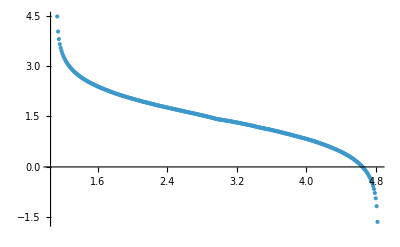

```mathematica
parteReKK1280=sskkrebook[omega1,k28Data,3,parteRe28[3]];
ListPlot[Transpose[{omega1,parteReKK1280}],PlotRange->All]
```

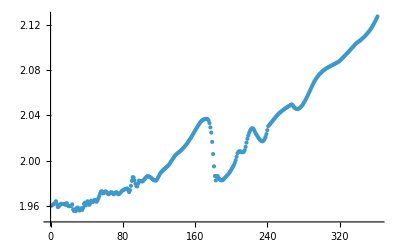

```mathematica
prueba=Table[epsRe[parteRe28,parteIm28,x],{x,1.19,4.8,0.01}];
ListPlot[prueba]
```

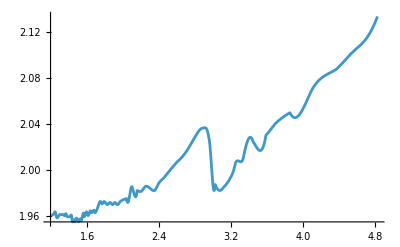

```mathematica
Plot[{epsRe[parteRe28,parteIm28,x]},{x,1.19,4.83},PlotRange->All]
```

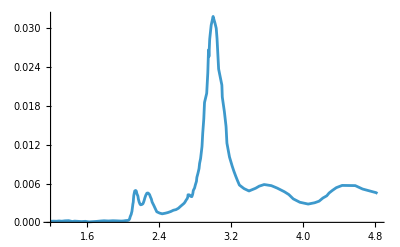

```mathematica
Plot[{epsIm[parteRe28,parteIm28,x]},{x,1.19,4.83},PlotRange->All]
```

```mathematica
(*Intervalos de búsqueda de los máximos*)
intervalos28={{2.1,2.2},{2.2,2.4},{2.8,3.3},{3.5,3.8},{4,4.7}};
eps28[x_]:=epsIm[parteRe28,parteIm28,x];
ω0i28=ω0i[eps28,intervalos28];
```

```mathematica
(*Ajuste de la parte imaginaria con lorentzianas*)
{xmin,xmax}={Min[datos2Im],Max[datos2Im]};
(*Datos para ajuste*)
eps28Data0=Table[{x,eps28[x]},{x,xmin,2.65,0.01}];
eps28Data1=Table[{x,eps28[x]},{x,2.76,xmax,0.01}];
eps28Data2=Join[eps28Data0,eps28Data1];
```

InterpolatingFunction::dmval: Input value {4.83} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.84} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.85} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
xmax
```

4.88176

InterpolatingFunction::dmval: Input value {4.8263} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.8363} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.8463} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

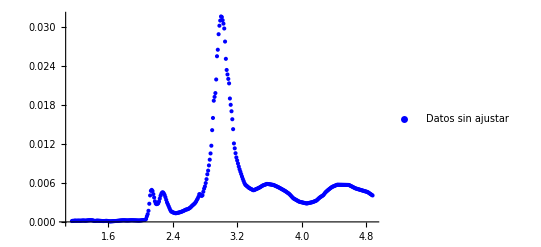

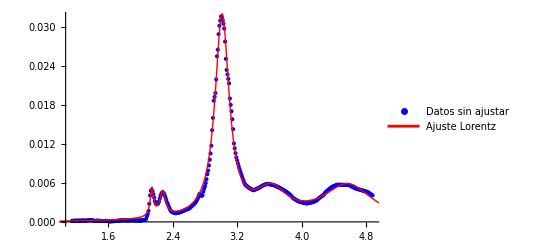

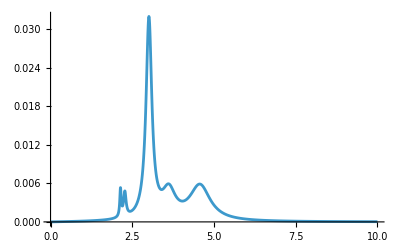

fit280[BestFitParameters]

```mathematica
(*Datos para ajuste*)
eps28Data=Table[{x,eps28[x]},{x,xmin,xmax,0.01}];
(* Ajustar con NonlinearModelFit*)
fit28Big=NonlinearModelFit[eps28Data,lorentzSumIm[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5],{{A1,0.01},{ω01,ω0i28[[1]]},{γ1,0.05},{A2,0.01},{ω02,ω0i28[[2]]},{γ2,0.1},{A3,0.01},{ω03,ω0i28[[3]]},{γ3,0.05},{A4,0.01},{ω04,ω0i28[[4]]},{γ4,0.1},{A5,0.01},{ω05,ω0i28[[5]]},{γ5,0.1}},ω];

(*Grafica datos originales y ajuste con 5 Lorentzianas*)
ListPlot[eps28Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All]
Show[ListPlot[eps28Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit28Big[ω],{ω,xmin-0.5,xmax+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit28Big[ω],{ω,0,10},PlotRange->All]
ScientificForm[fit280["BestFitParameters"],3]
```

```mathematica
residuals=({#[[1]],#[[2]]-fit28Big[#[[1]]]}&)/@eps28Data;
fitSmall=NonlinearModelFit[residuals,{A lorentzIm[ω,ω0,γ],A>0 &&γ>0 &&2.75>ω0>2.70},{{A,0.005},{ω0,2.73},{γ,0.0}},ω];
```

```mathematica
fitSmall["BestFitParameters"]
```

{A→0.0106169,ω0→2.725,γ→2155.77}

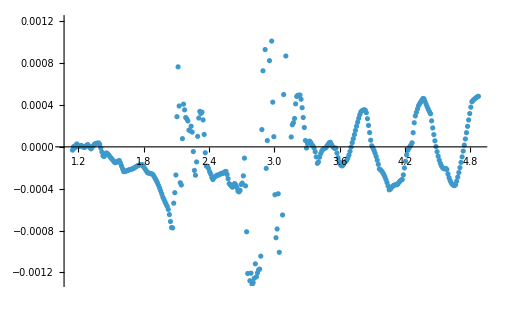

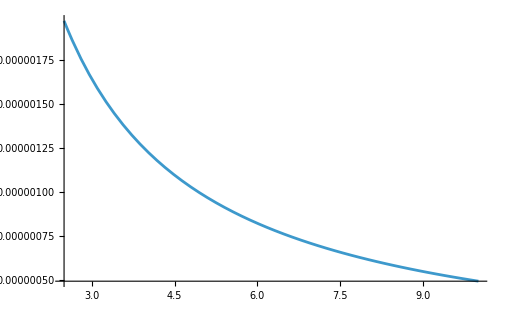

```mathematica
ListPlot[residuals]
Plot[fitSmall[x],{x,2.5,10}]
```

```mathematica
fit280["BestFitParameters"]
```

fit280[BestFitParameters]

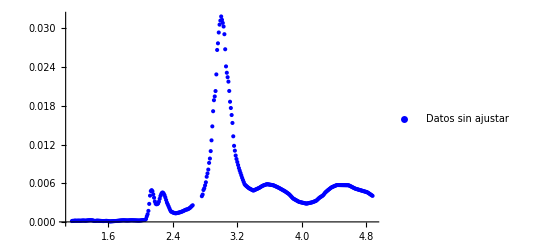

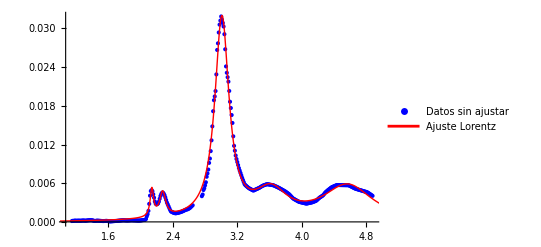

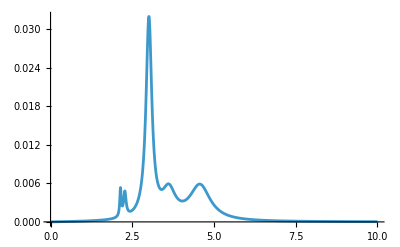

{A1→4.73×10^-4,ω01→2.14,γ1→5.15×10^-2,A2→7.85×10^-4,ω02→2.27,γ2→9.11×10^-2,A3→2.×10^-2,ω03→3.01,γ3→2.13×10^-1,A4→7.52×10^-3,ω04→3.63,γ4→4.88×10^-1,A5→1.92×10^-2,ω05→4.59,γ5→7.64×10^-1}

```mathematica
fit28Sin6=NonlinearModelFit[eps28Data2,lorentzSumIm[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5],{{A1,0.01},{ω01,ω0i28[[1]]},{γ1,0.05},{A2,0.01},{ω02,ω0i28[[2]]},{γ2,0.1},{A3,0.01},{ω03,ω0i28[[3]]},{γ3,0.05},{A4,0.01},{ω04,ω0i28[[4]]},{γ4,0.1},{A5,0.01},{ω05,ω0i28[[5]]},{γ5,0.1}},ω];

(*Grafica datos originales y ajuste con 5 Lorentzianas*)
ListPlot[eps28Data2,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All]
Show[ListPlot[eps28Data2,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit28Sin6[ω],{ω,xmin-0.5,xmax+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit28Sin6[ω],{ω,0,10},PlotRange->All]
ScientificForm[fit28Sin6["BestFitParameters"],3]
```

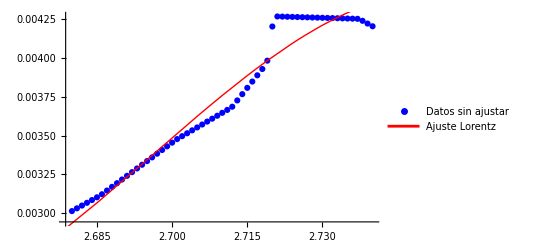

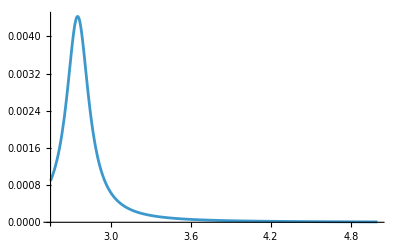

{A1→2.49×10^-3,ω01→2.75,γ1→2.04×10^-1}

```mathematica
eps28Data3=Table[{x,eps28[x]},{x,2.68,2.74,0.001}];
fit281=NonlinearModelFit[eps28Data3,A1*lorentzIm[ω,ω01,γ1],{{A1,0.0001},{ω01,2.7},{γ1,0.005}},ω];
Show[ListPlot[eps28Data3,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit281[ω],{ω,2.55,3.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit281[ω],{ω,2.55,5},PlotRange->All]
ScientificForm[fit281["BestFitParameters"],3]
```

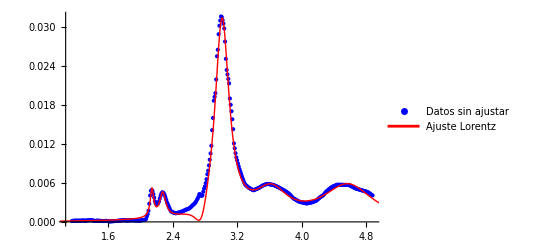

Plot::pllim: Range specification {ω,0.1} is not of the form {x, xmin, xmax}.

Plot[fit286[ω],{ω,0.1},PlotRange→All]

```mathematica
fit286[x_]:=fit28Sin6[x]-fit281[x]
Show[ListPlot[eps28Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit286[ω],{ω,xmin-0.5,xmax+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit286[ω],{ω,0.10},PlotRange->All]
```

```mathematica
fit28tot2=NonlinearModelFit[eps28Data,{fit28Big[x]+A*fit281[x],A>0 },{{A,0.1}},x];
```

```mathematica
ScientificForm[fit28tot2["BestFitParameters"],3]
```

{A→9.4×10^-5}

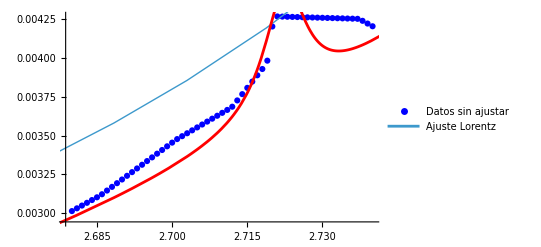

```mathematica
Show[ListPlot[eps28Data3,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
Plot[{fit28tot2[ω],fit28tot[ω]},{ω,2,2.75},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
```

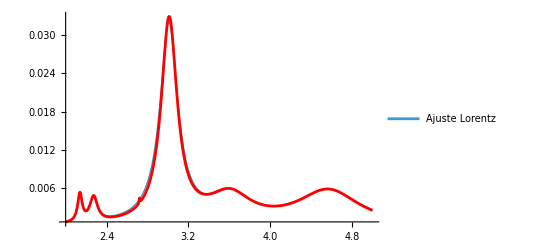

```mathematica
Plot[{fit28tot2[ω],fit28tot[ω]},{ω,2,5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]
```

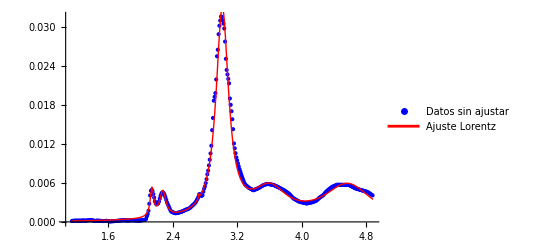

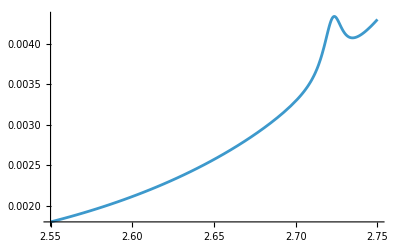

{A1→4.87×10^-4,ω01→2.14,γ1→5.24×10^-2,A2→8.23×10^-4,ω02→2.27,γ2→9.27×10^-2,A3→1.81×10^-2,ω03→3.01,γ3→1.88×10^-1,A4→8.47×10^-3,ω04→3.61,γ4→5.22×10^-1,A5→1.86×10^-2,ω05→4.58,γ5→7.37×10^-1,A6→2.62×10^-5,ω06→2.72,γ6→1.41×10^-2}

```mathematica
fit28tot=NonlinearModelFit[eps28Data,{lorentzSumIm6[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6],A6>0&&0.2>γ6>0&&2.76>ω06>2.66},{{A1,0.0004782178157627876},{ω01,2.137912709290393},{γ1,0.05151114401225601},{A2,0.0008796830663224468},{ω02,2.272168824653029},{γ2,0.10157583527502236},{A3,0.01887353896785414},{ω03,3.0020747706505286},{γ3,0.20241983912383665},{A4,0.008372231895518993},{ω04,3.5976753121279126},{γ4,0.5543539945895241},{A5,0.01947090645782093},{ω05,4.5748},{γ5,0.7793767158328045},{A6,0.00179},{ω06,2.73},{γ6,0.154}},ω,Weights->(If[2.6<#<2.8,100,2]&/@(eps28Data[[All,1]]))
];
Show[ListPlot[eps28Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit28tot[ω],{ω,xmin,xmax},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit28tot[ω],{ω,2.55,2.75},PlotRange->All]
ScientificForm[fit28tot["BestFitParameters"],3]
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 1.02452×10^-6.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

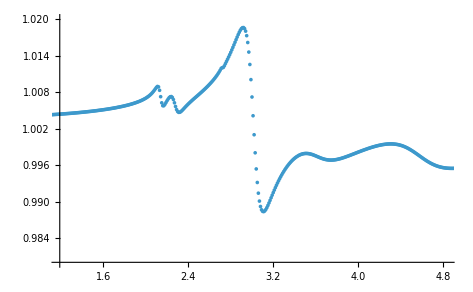

```mathematica
parteIm0282=Table[fit28tot[x],{x,0,10,0.01}];
parteReKK1282=kkrebook[omega,parteIm0282];
ListPlot[Transpose[{omega,parteReKK1282}],PlotRange->{{1.19,4.83},{0.98,1.02}}]
```

```mathematica
h c/1
```

1240.7

```mathematica
lorentzIm[ω_,ω0_,γ_]:=(γ ω)/((ω0^2-ω^2)^2+(γ ω)^2)
```

```mathematica
lorentz[w_,w0_,g_,A_]:=(A)/((w0^2-w^2)-(I *g* w))
```

```mathematica
lorentz6[w_,w01_,g1_,A1_,w02_,g2_,A2_,w03_,g3_,A3_,w04_,g4_,A4_,w05_,g5_,A5_,w06_,g6_,A6_]:=lorentz[w,w01,g1,A1]+lorentz[w,w02,g2,A2]+lorentz[w,w03,g3,A3]+lorentz[w,w04,g4,A4]+lorentz[w,w05,g5,A5]+lorentz[w,w06,g6,A6];
```

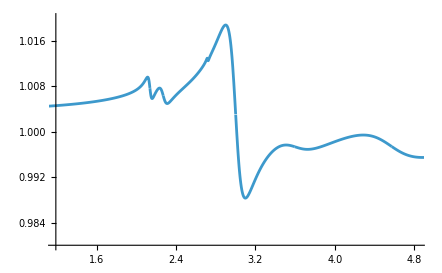

```mathematica
Plot[Re[1+lorentz6[omega,2.137912709290393,0.05151114401225601,0.0004782178157627876,2.272168824653029,0.10157583527502236,0.0008796830663224468,3.0020747706505286,0.2024198391238366,0.01887353896785414,3.5976753121279126,0.5543539945895241,0.008372231895518993,4.5748,0.7793767158328045,0.01947090645782093,2.72,0.013,0.0000265]],{omega,0,10},PlotRange->{{1.19,4.83},{0.98,1.02}},PlotPoints->1000]
```

```mathematica
lorentz6[1,2.137912709290393,0.05151114401225601,0.0004782178157627876,2.272168824653029,0.10157583527502236,0.0008796830663224468,3.0020747706505286,0.2024198391238366,0.01887353896785414,3.5976753121279126,0.5543539945895241,0.008372231895518993,4.5748,0.7793767158328045,0.01947090645782093,2.72,0.013,0.0000265]
```

0.00437829+0.000137182 ⅈ

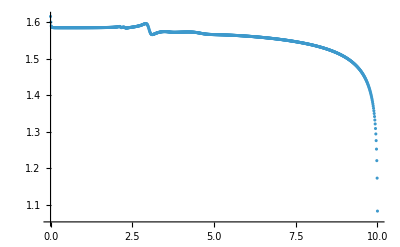
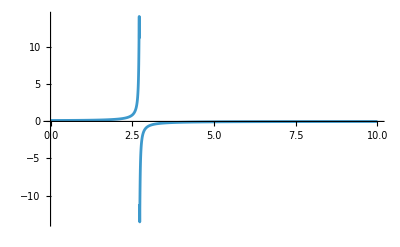
Show .08[-Graphics-,-Graphics-]

```mathematica
Show.08[ListPlot[Transpose[{omega,eps28KK[[1]]}],PlotRange->All],Plot[Re[lorentz[omega,2.72,0.013,1]],{omega,0,10},PlotRange->All]]
```

```mathematica
Im[lorentz[w,2.72,0.013,1]]
```

Im[1/(7.3984-(0.+0.013 ⅈ) w-w^2)]

```mathematica
lorentzIm[w,2.72,0.013]
```

(0.013 w)/(0.000169 w^2+(7.3984-w^2)^2)

```mathematica
epsRe[parteRe28,parteIm28,3.4]
```

2.02794

```mathematica
(*Obtención de la parte real a partir de la parte imaginaria con KK*)
omegass=Range[xmin,xmax,0.01];
parteReKK1280=sskkrebook[omegass,eps28Data[[All,2]],3.4,epsRe[parteRe28,parteIm28,3.4]];
ListPlot[Transpose[{omegass,parteReKK1280}],PlotRange->All]
```

Set::setraw: Cannot assign to raw object {1.1463,1.1563,1.1663,1.1763,1.1863,1.1963,1.2063,1.2163,1.2263,1.2363,1.2463,1.2563,1.2663,1.2763,«24»,1.5263,1.5363,1.5463,1.5563,1.5663,1.5763,1.5863,1.5963,1.6063,1.6163,1.6263,1.6363,«324»}.

Set::setraw: Cannot assign to raw object 0.000130412.

Set::setraw: Cannot assign to raw object 0.000166652.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Part::pspec1: Part specification NotFound is not applicable.

-Graphics-

Set::setraw: Cannot assign to raw object {1.1463,1.1563,1.1663,1.1763,1.1863,1.1963,1.2063,1.2163,1.2263,1.2363,1.2463,1.2563,1.2663,1.2763,«24»,1.5263,1.5363,1.5463,1.5563,1.5663,1.5763,1.5863,1.5963,1.6063,1.6163,1.6263,1.6363,«324»}.

Set::setraw: Cannot assign to raw object {1.00434,1.00432,1.00431,1.0043,1.00429,1.00428,1.00429,1.0043,1.0043,1.0043,1.00431,1.00433,1.00434,1.00435,«23»,1.00464,1.00467,1.0047,1.00473,1.00476,1.00478,1.00479,1.0048,1.00482,1.00485,1.0049,1.00495,1.00499,«324»}.

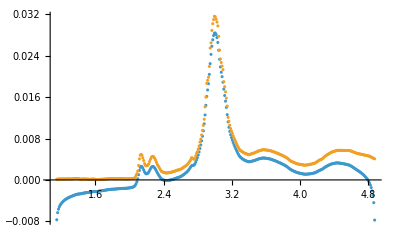

```mathematica
(*Obtención de la parte imaginaria a partir de la real obtenida con KK*)
parteImKK1280=kkimbook[omegass,parteReKK1280];
ListPlot[{Transpose[{omegass,parteImKK1280}],Transpose[{omegass,eps28Data[[All,2]]}]},PlotRange->All]
```

```mathematica
eps30KK=selfconsbook[omegass,parteReKK1280,eps28Data[[All,2]],10,0.5];
```

Set::setraw: Cannot assign to raw object {1.1463,1.1563,1.1663,1.1763,1.1863,1.1963,1.2063,1.2163,1.2263,1.2363,1.2463,1.2563,1.2663,1.2763,«24»,1.5263,1.5363,1.5463,1.5563,1.5663,1.5763,1.5863,1.5963,1.6063,1.6163,1.6263,1.6363,«324»}.

Set::setraw: Cannot assign to raw object {1.00434,1.00432,1.00431,1.0043,1.00429,1.00428,1.00429,1.0043,1.0043,1.0043,1.00431,1.00433,1.00434,1.00435,«23»,1.00464,1.00467,1.0047,1.00473,1.00476,1.00478,1.00479,1.0048,1.00482,1.00485,1.0049,1.00495,1.00499,«324»}.

Set::setraw: Cannot assign to raw object 0.000130412.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

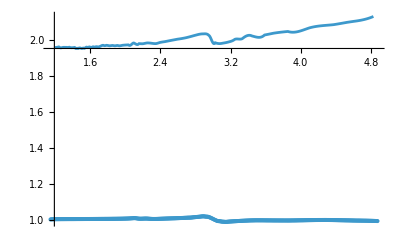

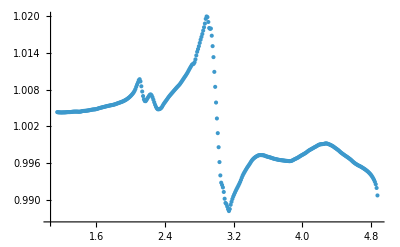

```mathematica
Show[Plot[{epsRe[parteRe28,parteIm28,x]},{x,1.19,4.83},PlotRange->All],ListPlot[{Transpose[{omegass,eps30KK[[1]]}]},PlotRange->All]]
ListPlot[{Transpose[{omegass,parteReKK1280}]},PlotRange->All]
```

## Drude

## Funciones generales

```mathematica
(*Función que devuelve la parte real y la imaginaria de la función dieléctrica a partir del índice de refracción*)
epsRe[parteRe_,parteIm_,x_]:=parteRe[x]^2-parteIm[x]^2;
epsIm[parteRe_,parteIm_,x_]:=(2*parteRe[x]*parteIm[x]);
(*Función para encontrar los máximos alrededor de intervalos dados*)
ω0i[eps_,intervalos_]:=GoldenSearchMax[eps,##]&@@@intervalos;
(*Parte imaginaria de lorentziana*)
lorentzIm[ω_,ω0_,γ_]:=(γ ω)/((ω0^2-ω^2)^2+(γ ω)^2)
(*Parte imaginaria de drude*)
drudeIm[ω_,γ_]:=(γ)/(ω+(ω^2+γ^2))
(*Definición de 5 lorentzianas*)
lorentzSumIm5[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_]:=A1 lorentzIm[ω,ω01,γ1]+A2 lorentzIm[ω,ω02,γ2]+A3 lorentzIm[ω,ω03,γ3]+ A4 lorentzIm[ω,ω04,γ4]+ A5 lorentzIm[ω,ω05,γ5];
(*Definición de 6 lorentzianas*)
lorentzSumIm6[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_,A6_,ω06_,γ6_]:=A1 lorentzIm[ω,ω01,γ1]+A2 lorentzIm[ω,ω02,γ2]+A3 lorentzIm[ω,ω03,γ3]+ A4 lorentzIm[ω,ω04,γ4]+ A5 lorentzIm[ω,ω05,γ5]+A6 lorentzIm[ω,ω06,γ6];
(*Definición de 6 lorentzianas + Drude*)
lorentzSumIm6Drude[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_,A6_,ω06_,γ6_,A7_,γ7_]:=A1 lorentzIm[ω,ω01,γ1]+A2 lorentzIm[ω,ω02,γ2]+A3 lorentzIm[ω,ω03,γ3]+ A4 lorentzIm[ω,ω04,γ4]+ A5 lorentzIm[ω,ω05,γ5]+A6 lorentzIm[ω,ω06,γ6]+A7 drudeIm[ω,γ7];
(*Definición de 4 lorentzianas*)
lorentzSumIm4[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_]:=A1 lorentzIm[ω,ω01,γ1]+A2 lorentzIm[ω,ω02,γ2]+A3 lorentzIm[ω,ω03,γ3]+A4 lorentzIm[ω,ω04,γ4];

(*Parte real de lorentziana*)
lorentzRe[A_,ω_,ω0_,γ_]:=1+(A *(ω0^2-ω^2))/((ω0^2-ω^2)^2+(γ ω)^2)
(*Definición de 5 lorentzianas*)
lorentzSumRe5[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_]:= lorentzRe[A1,ω,ω01,γ1]+lorentzRe[A2,ω,ω02,γ2]+ lorentzRe[A3,ω,ω03,γ3]+lorentzRe[A4,ω,ω04,γ4]+lorentzRe[A5,ω,ω05,γ5];
(*Definición de 4 lorentzianas*)
lorentzSumRe4[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_]:= lorentzRe[A1,ω,ω01,γ1]+lorentzRe[A2,ω,ω02,γ2]+ lorentzRe[A3,ω,ω03,γ3]+lorentzRe[A4,ω,ω04,γ4];
```

## Concentración 28.7 g/dL

```mathematica
(*Se van a importar los datos de la parte real e imaginaria del índice de refracción*)
datos0Im=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\28.7_k_ImN_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1Im=Drop[datos0Im,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2Im=h c/datos1Im[[All,1]];
(*Se interpolan los datos de la parte imaginaria y real*)
parteIm280=Transpose[{datos2Im,datos1Im[[All,2]]}];
parteIm28=Interpolation[parteIm280,InterpolationOrder->1];
(*Función que da la parte real del índice de refracción a partir de la relación de Meinke 2006*)
datosH2O=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\H2O_n.csv"];
datosBeta=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\Beta_parameter_ReN_Erythrocytes.csv"];
datos1Beta=Drop[datosBeta,1];
datos1H2O=Drop[datosH2O,1];
datos2Beta=h c/datos1Beta[[All,1]];
datos2H2O=h c/(datos1H2O[[All,1]]*1000);
beta=Interpolation[Transpose[{datos2Beta,datos1Beta[[All,2]]}]];
h2o=Interpolation[Transpose[{datos2H2O,datos1H2O[[All,2]]}]];
(*Se va a encontrar la parte real empleando la relación de Meinke 2006*)
parteRe[x_,C_]:=h2o[x]*((beta[x]*C)+1);
parteRe28[x_]:=parteRe[x,28.7];
```

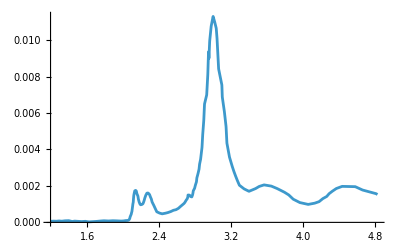

InterpolatingFunction::dmval: Input value {1.10008} lies outside the range of data in the interpolating function. Extrapolation will be used.

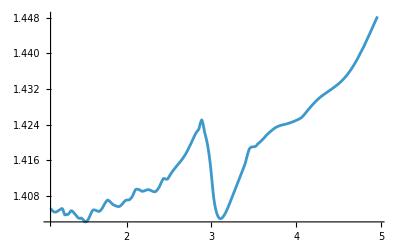

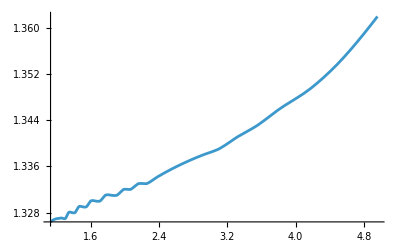

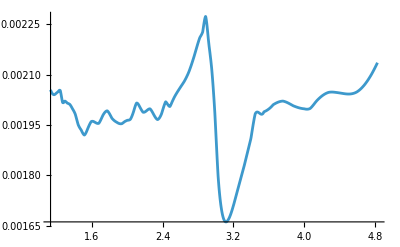

```mathematica
Plot[{parteIm28[x]},{x,1.19,4.83},PlotRange->All]
Plot[{parteRe28[x]},{x,1.1,4.96},PlotRange->All]
Plot[{h2o[x]},{x,1.13,4.96},PlotRange->All]
Plot[{beta[x]},{x,1.13,4.83},PlotRange->All]
```

```mathematica
h c/1150
```

1.07887

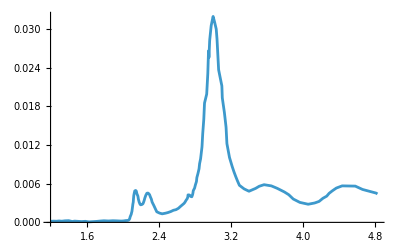

```mathematica
Plot[{epsIm[parteRe28,parteIm28,x]},{x,1.19,4.83},PlotRange->All]
```

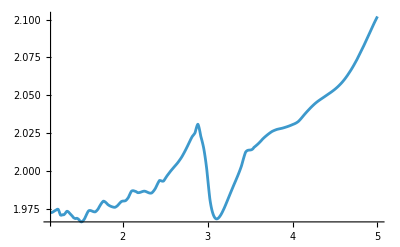

```mathematica
Plot[{epsRe[parteRe28,parteIm28,x]},{x,1.15,5},PlotRange->All]
```

```mathematica
(*Intervalos de búsqueda de los máximos*)
intervalos28={{2.1,2.2},{2.2,2.4},{2.8,3.3},{3.5,3.8},{4,4.7}};
eps28[x_]:=epsIm[parteRe28,parteIm28,x];
ω0i28=ω0i[eps28,intervalos28];
(*Ajuste de la parte imaginaria con lorentzianas*)
{xmin,xmax}={Min[datos2Im],Max[datos2Im]};
```

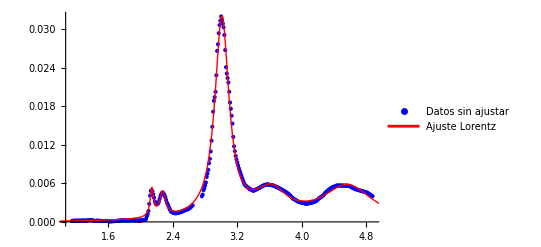

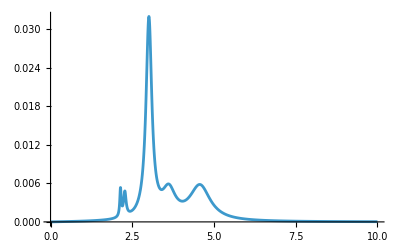

{A1→4.74×10^-4,ω01→2.14,γ1→5.15×10^-2,A2→7.89×10^-4,ω02→2.27,γ2→9.15×10^-2,A3→1.99×10^-2,ω03→3.01,γ3→2.13×10^-1,A4→7.52×10^-3,ω04→3.63,γ4→4.89×10^-1,A5→1.9×10^-2,ω05→4.59,γ5→7.64×10^-1}

{0.000474355,2.13957,0.0515139,0.000789019,2.2735,0.0915299,0.0198978,3.01086,0.212506,0.0075225,3.62506,0.489019,0.0190063,4.58734,0.763838}

```mathematica
(*Datos para ajuste ignorando el pico pequeño faltante*)
eps28Data0=Table[{x,eps28[x]},{x,xmin,2.65,0.01}];
eps28Data1=Table[{x,eps28[x]},{x,2.76,xmax,0.01}];
eps28Data2=Join[eps28Data0,eps28Data1];
eps28Data=Table[{x,eps28[x]},{x,xmin,xmax,0.01}];
(* Ajustar con NonlinearModelFit*)
fit28=NonlinearModelFit[eps28Data2,lorentzSumIm5[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5],{{A1,0.01},{ω01,ω0i28[[1]]},{γ1,0.05},{A2,0.01},{ω02,ω0i28[[2]]},{γ2,0.1},{A3,0.01},{ω03,ω0i28[[3]]},{γ3,0.05},{A4,0.01},{ω04,ω0i28[[4]]},{γ4,0.1},{A5,0.01},{ω05,ω0i28[[5]]},{γ5,0.1}},ω];
(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[eps28Data2,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit28[ω],{ω,xmin-0.5,xmax+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit28[ω],{ω,0,10},PlotRange->All]
ScientificForm[fit28["BestFitParameters"],3]
fit28Values=Values[fit28["BestFitParameters"]]
```

```mathematica
(*Datos para ajuste del pico pequeño*)
eps28Data3=Table[{x,eps28[x]},{x,2.68,2.74,0.001}];
fit281=NonlinearModelFit[eps28Data3,A1*lorentzIm[ω,ω01,γ1],{{A1,0.0001},{ω01,2.7},{γ1,0.005}},ω];
Show[ListPlot[eps28Data3,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit281[ω],{ω,2.55,3.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit281[ω],{ω,2.55,5},PlotRange->All]
ScientificForm[fit281["BestFitParameters"],3]
fit281Values=Values[fit281["BestFitParameters"]]
```

-Graphics-

-Graphics-

{A1→2.49×10^-3,ω01→2.75,γ1→2.04×10^-1}

{0.00248954,2.75493,0.204166}

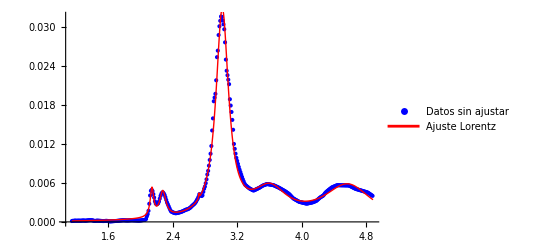

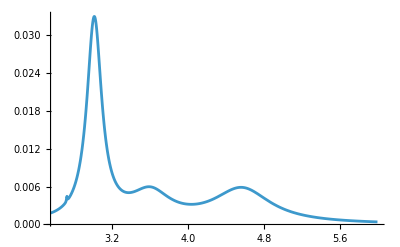

{A1→4.9×10^-4,ω01→2.14,γ1→5.25×10^-2,A2→-8.13×10^-4,ω02→2.27,γ2→-9.14×10^-2,A3→-1.82×10^-2,ω03→3.01,γ3→-1.89×10^-1,A4→-8.36×10^-3,ω04→3.61,γ4→-5.17×10^-1,A5→-1.84×10^-2,ω05→4.58,γ5→-7.37×10^-1,A6→2.18×10^-5,ω06→2.72,γ6→1.03×10^-2}

```mathematica
(*Datos para ajuste total*)
fit28tot=NonlinearModelFit[eps28Data,{lorentzSumIm6[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6],A6>0&&0.2>γ6>0&&2.77>ω06>2.66},{{A1,fit28Values[[1]]},{ω01,fit28Values[[2]]},{γ1,fit28Values[[3]]},{A2,fit28Values[[4]]},{ω02,fit28Values[[5]]},{γ2,fit28Values[[6]]},{A3,fit28Values[[7]]},{ω03,fit28Values[[8]]},{γ3,fit28Values[[9]]},{A4,fit28Values[[10]]},{ω04,fit28Values[[11]]},{γ4,fit28Values[[12]]},{A5,fit28Values[[13]]},{ω05,fit28Values[[14]]},{γ5,fit28Values[[15]]},{A6,fit281Values[[1]]},{ω06,fit281Values[[2]]},{γ6,fit281Values[[3]]}},ω,Weights->(If[2.6<#<2.8,73,2]&/@(eps28Data[[All,1]]))
];
Show[ListPlot[eps28Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit28tot[ω],{ω,xmin,xmax},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit28tot[ω],{ω,2.55,6},PlotRange->All]
ScientificForm[fit28tot["BestFitParameters"],3]
```

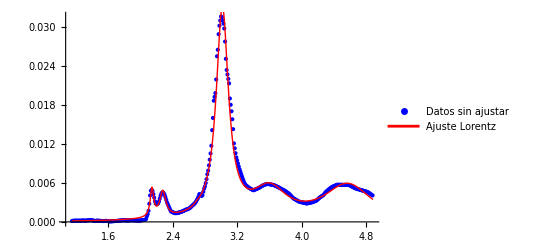

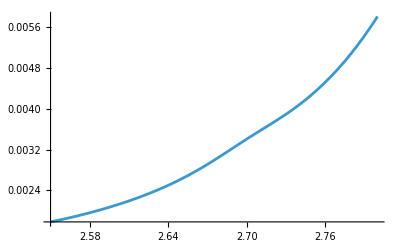

{A1→4.96×10^-4,ω01→2.14,γ1→5.33×10^-2,A2→8.1×10^-4,ω02→2.27,γ2→9.06×10^-2,A3→1.78×10^-2,ω03→3.01,γ3→1.84×10^-1,A4→8.52×10^-3,ω04→3.61,γ4→5.2×10^-1,A5→1.86×10^-2,ω05→4.58,γ5→7.33×10^-1,A6→7.05×10^-5,ω06→2.7,γ6→1.02×10^-1,A7→8.11×10^-1,γ7→2.×10^5}

```mathematica
(*Datos para ajuste total CON Drude*)
fit28tot=NonlinearModelFit[eps28Data,{lorentzSumIm6Drude[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6,A7,γ7],0.003>A6>0&&A1>0&&A2>0&&A3>0&&A4>0&&A5>0&&A7>0&&0.2>γ6>0.1&&2.77>ω06>2.66&&γ1>0&&2.3>ω02>2.2&&γ2>0&&γ3>0&&γ4>0&&γ5>0&&γ7>0},{{A1,fit28Values[[1]]},{ω01,fit28Values[[2]]},{γ1,0.05},{A2,fit28Values[[4]]},{ω02,fit28Values[[5]]},{γ2,0.05},{A3,fit28Values[[7]]},{ω03,fit28Values[[8]]},{γ3,0.000005},{A4,fit28Values[[10]]},{ω04,fit28Values[[11]]},{γ4,0.0005},{A5,fit28Values[[13]]},{ω05,fit28Values[[14]]},{γ5,0.0005},{A6,fit281Values[[1]]},{ω06,fit281Values[[2]]},{γ6,fit281Values[[3]]},{A7,0.0001},{γ7,0.05}},ω,Weights->(If[2.6<#<2.8,170,2]&/@(eps28Data[[All,1]]))
];
Show[ListPlot[eps28Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit28tot[ω],{ω,xmin,xmax},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit28tot[ω],{ω,2.55,2.8},PlotRange->All]
ScientificForm[fit28tot["BestFitParameters"],3]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

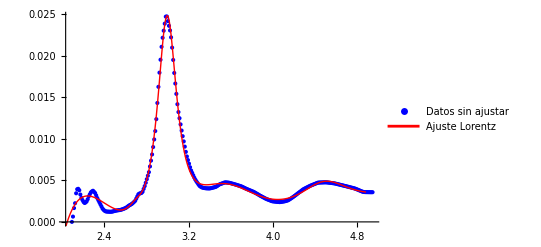

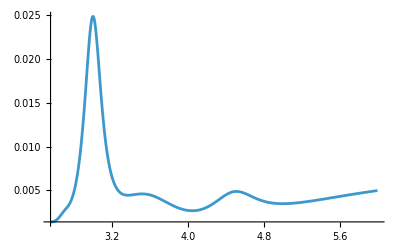

{A1→7.87×10^-1,ω01→1.91,γ1→2.01,A2→3.08,ω02→1.01,γ2→-3.29,A3→1.87×10^-2,ω03→3.,γ3→2.32×10^-1,A4→4.06×10^-2,ω04→3.55,γ4→1.11,A5→1.04×10^-2,ω05→4.5,γ5→6.31×10^-1,A6→7.06×10^-4,ω06→2.7,γ6→1.98×10^-1,A7→1.11,γ7→1.35}

```mathematica
fit15tot=NonlinearModelFit[eps15Data,{lorentzSumIm6Drude[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6,A7,γ7],0.002>A6>0&&0.2>γ6>0&&2.77>ω06>2.66&&A1>0&&A2>0&&A3>0&&A4>0&&A5>0&&A7>0&&γ7>0&&γ1>0},{{A1,fit15Values[[1]]},{ω01,fit15Values[[2]]},{γ1,fit15Values[[3]]},{A2,fit15Values[[4]]},{ω02,fit15Values[[5]]},{γ2,0.0005},{A3,fit15Values[[7]]},{ω03,fit15Values[[8]]},{γ3,fit15Values[[9]]},{A4,fit15Values[[10]]},{ω04,fit15Values[[11]]},{γ4,fit15Values[[12]]},{A5,fit15Values[[13]]},{ω05,fit15Values[[14]]},{γ5,fit15Values[[15]]},{A6,fit151Values[[1]]},{ω06,fit151Values[[2]]},{γ6,fit151Values[[3]]},{A7,0.0001},{γ7,0.05}},ω,Weights->(If[2.6<#<2.8,150,2]&/@(eps15Data[[All,1]]))
];
Show[ListPlot[eps15Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit15tot[ω],{ω,xmin,xmax},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit15tot[ω],{ω,2.55,6},PlotRange->All]
ScientificForm[fit15tot["BestFitParameters"],3]
```